```mathematica
x1=Table[i, {i, 50,150,1}];
n=Length[x1];
SeedRandom[n];
epsilon = RandomVariate[NormalDistribution[0,1], n];
SeedRandom[n];
x2=RandomVariate[PoissonDistribution[10],n];
y=11.11+1.58*x1+epsilon;
data= Transpose[{x1,x2,y}];
model=LinearModelFit[data, {xx1,xx2}, {xx1,xx2}];
f=model["Function"];

yHat = f[x1, x2]
(y-yHat).(y-yHat)/2/101
```

{90.33,90.9914,93.4941,95.3392,96.7897,97.5826,100.348,101.273,102.46,104.305,106.019,107.864,109.183,111.554,112.479,113.666,116.037,117.488,118.149,120.257,121.971,122.895,124.74,126.454,128.167,130.144,131.595,133.177,135.153,135.42,137.923,138.321,141.087,142.274,143.856,145.438,147.415,148.471,150.316,152.293,152.559,155.062,156.381,157.569,160.466,162.048,163.104,164.686,165.61,167.324,168.511,171.277,172.596,173.52,175.497,177.211,178.267,180.638,182.351,183.67,185.384,187.229,188.416,189.735,191.449,191.979,194.876,195.932,197.383,199.096,200.81,202.918,204.105,205.161,207.795,209.114,210.828,212.278,213.203,214.916,216.762,217.686,219.4,221.508,223.484,225.066,226.517,227.573,228.629,230.605,232.582,234.032,235.483,237.591,237.332,240.755,241.943,243.919,245.107,247.215,249.06}

0.376586

```mathematica
data2 = Transpose[{x1,y}];
model2=LinearModelFit[data2, {xx1}, {xx1}];
model2["RSquared"];
yhat2 = model2["Function"][x1];
```

```mathematica
yhat2;
(y-yhat2).(y-yhat2)/2/101
```

0.468857

```mathematica
0.9995588181818541
f
```

0.999559

12.4118+1.58204 #1-0.131519 #2&

```mathematica
%61["BestFit"]
```

11.1705+1.58096 xx1

0.376586

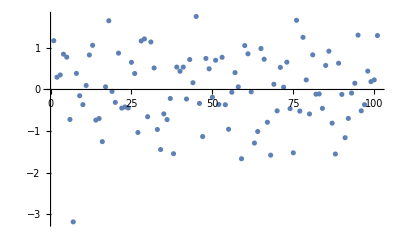

```mathematica
0.3765863780472114
ListPlot[y-yHat]
```

```mathematica
model
Export["D:\\code\\github\\微信公众号\\mechine_learning\\week_1\\train.dat", data, "CSV"]
```

FittedModel[12.4118+1.58204 xx1-0.131519 xx2]

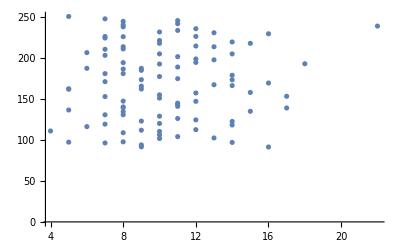

```mathematica
ListPlot[data[[All, {2,3}]]]
```

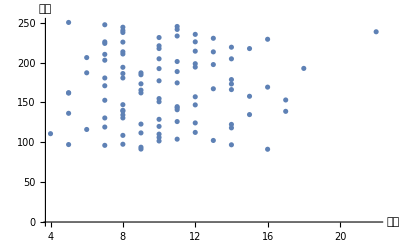

```mathematica
Show[%28,AxesLabel->{HoldForm[层数],HoldForm[房价]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

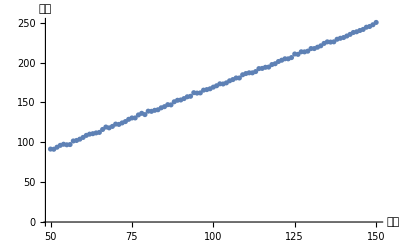

0.376586

```mathematica
Show[%26,AxesLabel->{HoldForm[大小],HoldForm[房价]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
pythonf = 1.14+1.64#1+0.34 #2&
```

1.14+1.64 #1+0.34 #2&

```mathematica
pythonY = pythonf[x1,x2]
```

{86.2,90.22,89.48,90.44,92.42,96.1,94.68,98.02,100.68,101.64,102.94,103.9,106.22,105.82,109.16,111.82,111.42,113.4,117.42,117.7,119.,122.34,123.3,124.6,125.9,126.52,128.5,130.14,130.76,135.8,135.06,139.76,138.34,141.,142.64,144.28,144.9,147.9,148.86,149.48,154.52,153.78,156.1,158.76,157.,158.64,161.64,163.28,166.62,167.92,170.58,169.16,171.48,174.82,175.44,176.74,179.74,179.34,180.64,182.96,184.26,185.22,187.88,190.2,191.5,195.86,194.1,197.1,199.08,200.38,201.68,201.96,204.62,207.62,206.54,208.86,210.16,212.14,215.48,216.78,217.74,221.08,222.38,222.66,223.28,224.92,226.9,229.9,232.9,233.52,234.14,236.12,238.1,238.38,244.78,241.66,244.32,244.94,247.6,247.88,248.84}

```mathematica
(y-pythonY).(y-pythonY)/2/101
```

3.39116

```mathematica
ybar = Mean[y]
```

169.267

```mathematica
IntegerPart[169.26653060800518]
```

169

```mathematica
sst= Total[(y-ybar)^2]
```

214671.

```mathematica
ssepython= Total[(yHat-ybar)^2]
```

214595.